```mathematica
ClearAll["Global`*"];
(*(*Su82002*)
ρ=1.123*10^3;  (*1[g/mL]=10^3[kg/m^3]*)
η=7.5*10^-6; (*1[cSt]=10^-6[m^2/s]*)*)
(*Su82005*)
ρ=1.164*10^3;  (*1[g/mL]=10^3[kg/m^3]*)
η=45*10^-6; (*1[cSt]=10^-6[m^2/s]*)
(*(*Su82010*)
ρ=1.187*10^3;  (*1[g/mL]=10^3[kg/m^3]*)
η=380*10^-6; (*1[cSt]=10^-6[m^2/s]*)*)
(*(*Su82025*)
ρ=1.219*10^3;  (*1[g/mL]=10^3[kg/m^3]*)
η=4500*10^-6; (*1[cSt]=10^-6[m^2/s]*)*)

V=4*10^-6; (*1 [mL]=10^-6[m^3]*)
A=π*(50*10^-3)^2; (*1[mm]=10^-3[m]*)
h0=V/A;
w0= 10.47; (*100RPM in[rads/s] *)
wstep=5;
K=ρ/(3*η);
h[t_,ω_]:=h0/((1+K*ω^2*h0^2*t)^(1/2))*10^9;
hexprlist={};
Legendlist={};
Do[AppendTo[hexprlist,h[t,i*wstep*w0]],{i,1,5}];
Do[AppendTo[Legendlist,"ω="<>TextString[i*wstep*100]<>"RPM"],{i,1,5}];
hexprlist
```

{1600000/(π √(1+6129.04 t)),1600000/(π √(1+24516.2 t)),1600000/(π √(1+55161.4 t)),1600000/(π √(1+98064.7 t)),1600000/(π √(1+153226. t))}

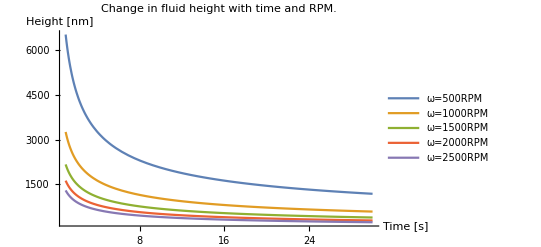

```mathematica
Plot [hexprlist,{t,1,30},AxesLabel->{"Time [s]","Height [nm]"},PlotRange->{0,All},PlotLabel->"Change in fluid height with time and RPM.",PlotLegends->Legendlist]
```